# Standard SIR Model

```mathematica
eq[β_,l_,i0_]:=NDSolve[{s'[t]==-β s[t] i[t],
i'[t] == β s[t] i[t]-i[t]/l,
r'[t] == i[t]/l,
s[0] == 1-i0,
i[0] == i0,
r[0] == 0
},{s,i,r},{t,0,250}]
```

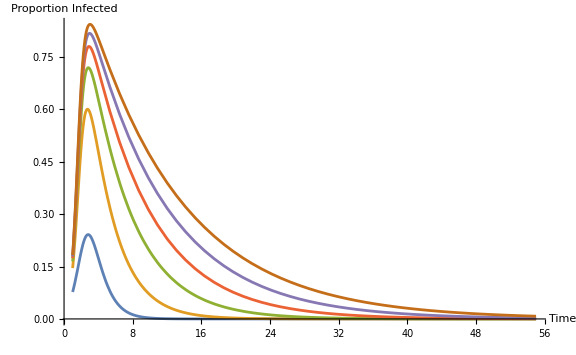

```mathematica
Plot[Evaluate[Table[i[τ]/.eq[2.5,β,0.02],{β,1,11,2}]],{τ,1,55}, PlotRange->All, AxesLabel->{"Time", "Proportion Infected"},
ImageSize->Large]
```

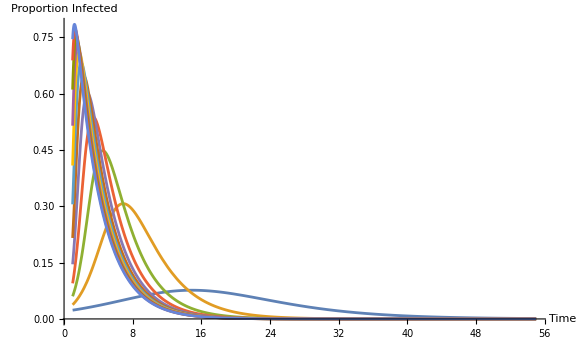

```mathematica
Plot[Evaluate[Table[i[τ]/.eq[l,3,0.02],{l,.5,6,.5}]],{τ,1,55}, PlotRange->All, AxesLabel->{"Time", "Proportion Infected"},
ImageSize->Large]
```